```mathematica
SetDirectory[NotebookDirectory[]];
a=Import["y_act.csv","Data"];
a=ArrayReshape[a,{20,20,100,4}];
p=Import["y_pred.csv","Data"];
p=ArrayReshape[p,{20,20,100,4}];
p1=Import["y_pred1.csv","Data"];
p1=ArrayReshape[p1,{20,20,100,4}];
p2=Import["y_pred2.csv","Data"];
p2=ArrayReshape[p2,{20,20,100,4}];
```

75

1

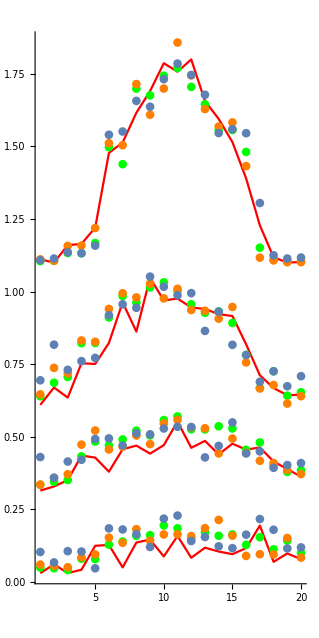

```mathematica
m=75
n=1
Show[ListLinePlot[a[[All,1,m,n]],PlotStyle->Red],
ListPlot[p[[All,1,m,n]],PlotStyle->Green],
ListPlot[p1[[All,1,m,n]],PlotStyle->Orange],
ListPlot[p2[[All,1,m,n]]],
ListLinePlot[0.3+a[[All,5,m,n]],PlotStyle->Red],
ListPlot[0.3+p[[All,5,m,n]],PlotStyle->Green],
ListPlot[0.3+p1[[All,5,m,n]],PlotStyle->Orange],
ListPlot[0.3+p2[[All,5,m,n]]],
ListLinePlot[0.6+a[[All,10,m,n]],PlotStyle->Red],
ListPlot[0.6+p[[All,10,m,n]],PlotStyle->Green],
ListPlot[0.6+p1[[All,10,m,n]],PlotStyle->Orange],
ListPlot[0.6+p2[[All,10,m,n]]],
ListLinePlot[1.1+a[[All,15,m,n]],PlotStyle->Red],
ListPlot[1.1+p[[All,15,m,n]],PlotStyle->Green],
ListPlot[1.1+p1[[All,15,m,n]],PlotStyle->Orange],
ListPlot[1.1+p2[[All,15,m,n]]],PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality"]
```

55

2

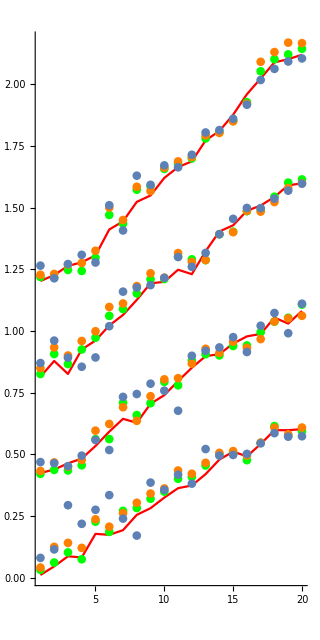

```mathematica
m=55
n=2
Show[ListLinePlot[a[[All,1,m,n]],PlotStyle->Red],
ListPlot[p[[All,1,m,n]],PlotStyle->Green],
ListPlot[p1[[All,1,m,n]],PlotStyle->Orange],
ListPlot[p2[[All,1,m,n]]],
ListLinePlot[0.4+a[[All,5,m,n]],PlotStyle->Red],
ListPlot[0.4+p[[All,5,m,n]],PlotStyle->Green],
ListPlot[0.4+p1[[All,5,m,n]],PlotStyle->Orange],
ListPlot[0.4+p2[[All,5,m,n]]],
ListLinePlot[0.8+a[[All,10,m,n]],PlotStyle->Red],
ListPlot[0.8+p[[All,10,m,n]],PlotStyle->Green],
ListPlot[0.8+p1[[All,10,m,n]],PlotStyle->Orange],
ListPlot[0.8+p2[[All,10,m,n]]],
ListLinePlot[1.2+a[[All,15,m,n]],PlotStyle->Red],
ListPlot[1.2+p[[All,15,m,n]],PlotStyle->Green],
ListPlot[1.2+p1[[All,15,m,n]],PlotStyle->Orange],
ListPlot[1.2+p2[[All,15,m,n]]],PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted]]
```

55

3

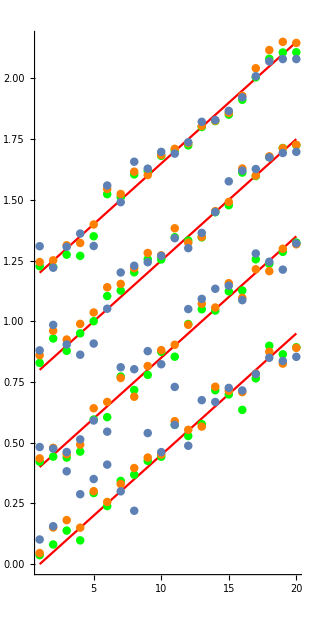

```mathematica
m=55
n=3
Show[ListLinePlot[a[[All,1,m,n]],PlotStyle->Red],
ListPlot[p[[All,1,m,n]],PlotStyle->Green],
ListPlot[p1[[All,1,m,n]],PlotStyle->Orange],
ListPlot[p2[[All,1,m,n]]],
ListLinePlot[0.4+a[[All,5,m,n]],PlotStyle->Red],
ListPlot[0.4+p[[All,5,m,n]],PlotStyle->Green],
ListPlot[0.4+p1[[All,5,m,n]],PlotStyle->Orange],
ListPlot[0.4+p2[[All,5,m,n]]],
ListLinePlot[0.8+a[[All,10,m,n]],PlotStyle->Red],
ListPlot[0.8+p[[All,10,m,n]],PlotStyle->Green],
ListPlot[0.8+p1[[All,10,m,n]],PlotStyle->Orange],
ListPlot[0.8+p2[[All,10,m,n]]],
ListLinePlot[1.2+a[[All,15,m,n]],PlotStyle->Red],
ListPlot[1.2+p[[All,15,m,n]],PlotStyle->Green],
ListPlot[1.2+p1[[All,15,m,n]],PlotStyle->Orange],
ListPlot[1.2+p2[[All,15,m,n]]],PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality"]
```

55

4

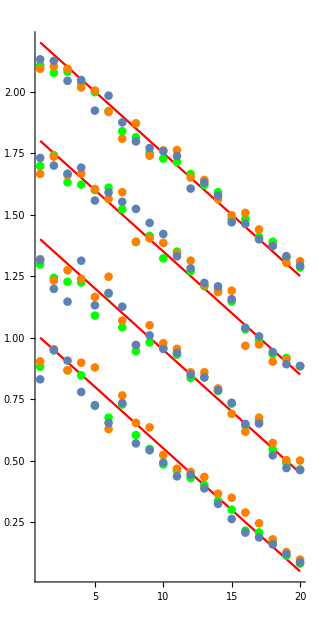

```mathematica
m=55
n=4
Show[ListLinePlot[a[[1,All,m,n]],PlotStyle->Red],
ListPlot[p[[1,All,m,n]],PlotStyle->Green],
ListPlot[p1[[1,All,m,n]],PlotStyle->Orange],
ListPlot[p2[[1,All,m,n]]],
ListLinePlot[0.4+a[[5,All,m,n]],PlotStyle->Red],
ListPlot[0.4+p[[5,All,m,n]],PlotStyle->Green],
ListPlot[0.4+p1[[5,All,m,n]],PlotStyle->Orange],
ListPlot[0.4+p2[[5,All,m,n]]],
ListLinePlot[0.8+a[[10,All,m,n]],PlotStyle->Red],
ListPlot[0.8+p[[10,All,m,n]],PlotStyle->Green],
ListPlot[0.8+p1[[10,All,m,n]],PlotStyle->Orange],
ListPlot[0.8+p2[[10,All,m,n]]],
ListLinePlot[1.2+a[[15,All,m,n]],PlotStyle->Red],
ListPlot[1.2+p[[15,All,m,n]],PlotStyle->Green],
ListPlot[1.2+p1[[15,All,m,n]],PlotStyle->Orange],
ListPlot[1.2+p2[[15,All,m,n]]],PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality"]
```